```mathematica
f[m_,b_]:=(m*Sqrt[b^3])/((b-m^2)^2)((3*Sqrt[b]*m)/Sqrt[b-m^2](ArcTan[m/Sqrt[b-m^2]]-Pi/2)+(2*b+m^2)/Sqrt[b])
```

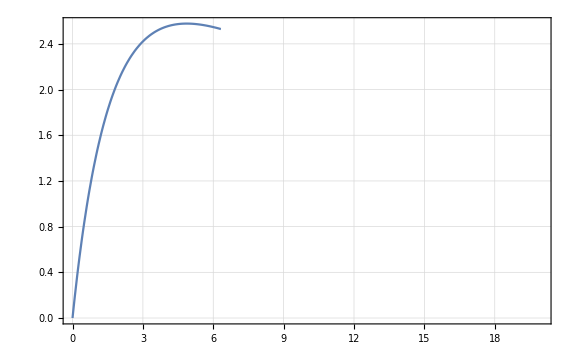

```mathematica
Plot[f[m,40],{m,0,20},GridLines->Automatic,Frame->True]
```

```mathematica
g[m_,b_]:=4*b*m^2(1/(b-m^2)+m*(ArcTan[m/Sqrt[b-m^2]]-Pi/2)/((b-m^2)^(3/2)))
```

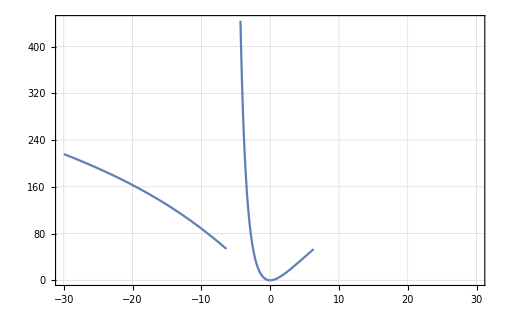

```mathematica
Plot[g[m,40],{m,-30,30},GridLines->Automatic,Frame->True]
```

```mathematica
h[m_,b_]:=2*m*Pi/(2*Pi)^2*(Sqrt[b/(b-m^2)]-1)
```

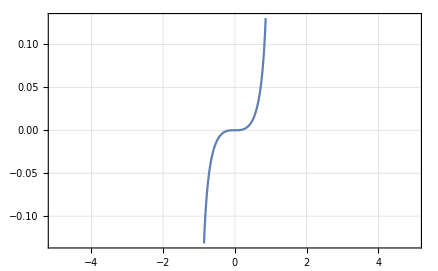

```mathematica
Plot[h[m,1],{m,-5,5},GridLines->Automatic,Frame->True]
```

```mathematica
w[b_,m_]:=-(8*b*m^2)/(b-m^2)-(ArcTan[m/Sqrt[b-m^2]]-Pi/2)*(8*b*m^3)/((b-m^2)^(3/2))
```

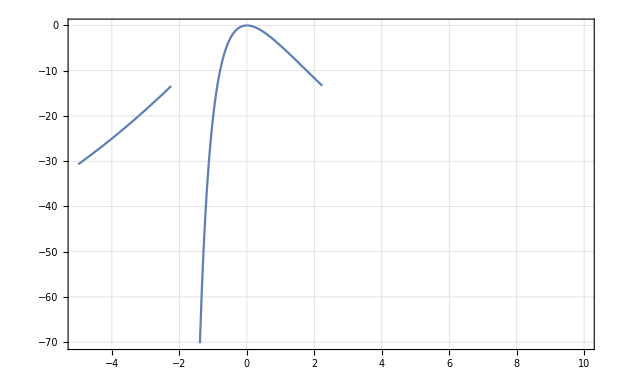

```mathematica
Plot[w[5,m],{m,-5,10},GridLines->Automatic,Frame->True]
```